## Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
SetOptions[Plot,Frame->True,ImageSize->Scaled[.7],FrameTicks->All,LabelStyle->Directive[FontSize->14,Black,FontOpacity->0.999,FontFamily->"Helvetica"],FrameTicksStyle->Directive[FontSize->12,Black,Plain],PlotPoints->200,PlotRange->All];
SetOptions[LogLinearPlot,Frame->True,ImageSize->Scaled[.7],FrameTicks->All,LabelStyle->Directive[FontSize->14,Black,FontOpacity->0.999,FontFamily->"Helvetica"],FrameTicksStyle->Directive[FontSize->12,Black,Plain],PlotPoints->200,PlotRange->All];
SetOptions[ListLogLinearPlot,Frame->True,ImageSize->Scaled[.7],FrameTicks->All,LabelStyle->Directive[FontSize->14,Black,FontOpacity->0.999,FontFamily->"Helvetica"],FrameTicksStyle->Directive[FontSize->12,Black,Plain],PlotRange->All];
SetOptions[ListLogLogPlot,Frame->True,ImageSize->Scaled[.7],FrameTicks->All,LabelStyle->Directive[FontSize->14,Black,FontOpacity->0.999,FontFamily->"Helvetica"],FrameTicksStyle->Directive[FontSize->12,Black,Plain],PlotRange->All];
```

## Testing

```mathematica
FreeSphericalWaveR[r_,k_,l_]:=√((2 k^2)/π) SphericalBesselJ[l,k r]
```

```mathematica
waves=Table[FreeSphericalWaveR[r,2π,l],{l,0,5}]
```

{2 √(2 π) SphericalBesselJ[0,2 π r],2 √(2 π) SphericalBesselJ[1,2 π r],2 √(2 π) SphericalBesselJ[2,2 π r],2 √(2 π) SphericalBesselJ[3,2 π r],2 √(2 π) SphericalBesselJ[4,2 π r],2 √(2 π) SphericalBesselJ[5,2 π r]}

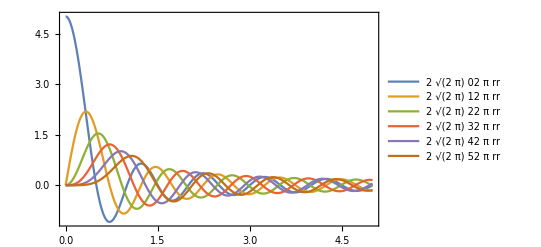

```mathematica
Plot[Evaluate[waves/.{r->rr}],{rr,0,5},PlotLegends->"Expressions"]
```

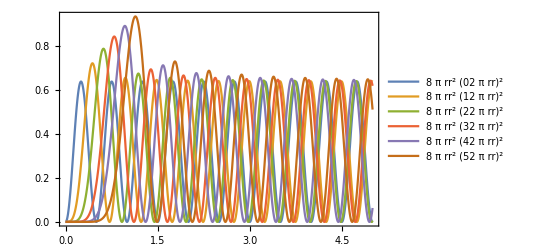

```mathematica
Plot[Evaluate[(rr waves/.{r->rr})^2],{rr,0,5},PlotLegends->"Expressions"]
```